AVGPMFArrayb3 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.237318,0.17485,0.115414,0.0725191,0.0445774,0.0271657,0.0165228,0.0100643,0.00614986,0.00377295,0.00232476,0.00143878,0.000894368,0.000558348,0.000350039,0.000220347,0.000139265,0.0000883677,0.0000562908,0.0000359965}}

AVGCDFArrayb3 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.522791,0.697642,0.813056,0.885575,0.930152,0.957318,0.97384,0.983905,0.990055,0.993828,0.996152,0.997591,0.998485,0.999044,0.999394,0.999614,0.999753,0.999842,0.999898,0.999934}}

AVGPMFArrayb10 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.219731,0.161445,0.106789,0.0673278,0.0416216,0.0256149,0.0158265,0.00986369,0.00621663,0.00396696,0.00256403,0.00167846,0.00111236,0.000745895,0.00050571,0.00034641,0.000239555,0.000167111,0.000117504,0.0000832204}}

AVGCDFArrayb10 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.55354,0.714985,0.821774,0.889102,0.930723,0.956338,0.972165,0.982028,0.988245,0.992212,0.994776,0.996454,0.997567,0.998313,0.998818,0.999165,0.999404,0.999571,0.999689,0.999772}}

28.3465

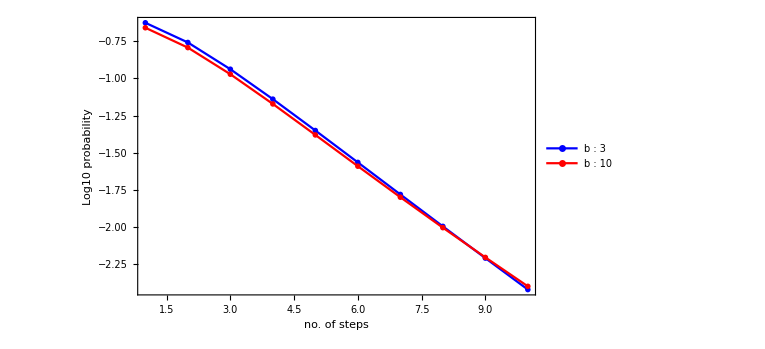

1-multi-PMF-psuccess05-b3b10-10nodeslog.eps

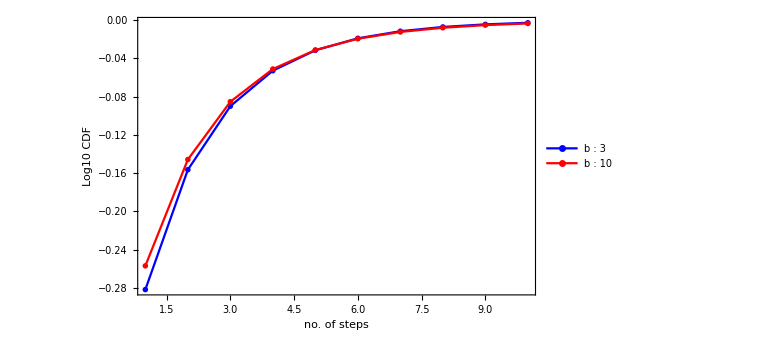

1-multi-CDF-psuccess05-b3b10-10nodeslog.eps

AVGCDFArrayb10 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.513004,0.68276,0.797768,0.871969,0.918846,0.948268,0.966756,0.978438,0.985877,0.990656,0.993756,0.995787,0.99713,0.998026,0.99863,0.999041,0.999323,0.999518,0.999653,0.999748}}

AVGPMFArrayb10 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.225202,0.169756,0.115008,0.0742015,0.0468773,0.0294213,0.0184883,0.0116819,0.00743882,0.00477949,0.00310019,0.00203051,0.00134284,0.000896551,0.000604152,0.000410768,0.000281681,0.000194734,0.000135658,0.0000951807}}

AVGCDFArrayb3 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.4184,0.591894,0.722783,0.814583,0.876194,0.916558,0.942708,0.959598,0.970529,0.977639,0.982295,0.985366,0.987409,0.988779,0.989705,0.990336,0.990769,0.991069,0.991278,0.991424}}

AVGPMFArrayb3 is : {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{0.204873,0.173494,0.130889,0.0917995,0.0616114,0.0403637,0.0261497,0.0168903,0.0109314,0.00710998,0.00465544,0.00307151,0.00204284,0.00136985,0.000926077,0.000631068,0.000433356,0.000299783,0.000208833,0.000146433}}

28.3465

```mathematica
(* if you want to rerun this code, don't forget to change the path of files to be imported; they are no longer in toor; they are in the same folder that this file is *)
(* at first importing all the data, produced in the files for separated 10 topologies *)

(* topology 1 *)
singlePMFArray1b3=Import["singlePMFArray1b3.mx"];
singlePMFArray2b10=Import["singlePMFArray2b10.mx"];

singleCDFArray1b3=Import["singleCDFArray1b3.mx"];
singleCDFArray2b10=Import["singleCDFArray2b10.mx"];

(* topology 3 *)
singlePMFArray3b3=Import["singlePMFArray3b3.mx"];
singlePMFArray4b10=Import["singlePMFArray4b10.mx"];

singleCDFArray3b3=Import["singleCDFArray3b3.mx"];
singleCDFArray4b10=Import["singleCDFArray4b10.mx"];

(* topology 4 *)
singlePMFArray5b3=Import["singlePMFArray5b3.mx"];
singlePMFArray6b10=Import["singlePMFArray6b10.mx"];

singleCDFArray5b3=Import["singleCDFArray5b3.mx"];
singleCDFArray6b10=Import["singleCDFArray6b10.mx"];

(* topology 5 *)
singlePMFArray7b3=Import["singlePMFArray7b3.mx"];
singlePMFArray8b10=Import["singlePMFArray8b10.mx"];

singleCDFArray7b3=Import["singleCDFArray7b3.mx"];
singleCDFArray8b10=Import["singleCDFArray8b10.mx"];

(* topology 6 *)
singlePMFArray9b3=Import["singlePMFArray9b3.mx"];
singlePMFArray10b10=Import["singlePMFArray10b10.mx"];

singleCDFArray9b3=Import["singleCDFArray9b3.mx"];
singleCDFArray10b10=Import["singleCDFArray10b10.mx"];

(* topology 7 *)
singlePMFArray11b3=Import["singlePMFArray11b3.mx"];
singlePMFArray12b10=Import["singlePMFArray12b10.mx"];

singleCDFArray11b3=Import["singleCDFArray11b3.mx"];
singleCDFArray12b10=Import["singleCDFArray12b10.mx"];

(* topology 8 *)
singlePMFArray13b3=Import["singlePMFArray13b3.mx"];
singlePMFArray14b10=Import["singlePMFArray14b10.mx"];

singleCDFArray13b3=Import["singleCDFArray13b3.mx"];
singleCDFArray14b10=Import["singleCDFArray14b10.mx"];

(* topology 9 *)
singlePMFArray15b3=Import["singlePMFArray15b3.mx"];
singlePMFArray16b10=Import["singlePMFArray16b10.mx"];

singleCDFArray15b3=Import["singleCDFArray15b3.mx"];
singleCDFArray16b10=Import["singleCDFArray16b10.mx"];

(* topology 10 *)
singlePMFArray17b3=Import["singlePMFArray17b3.mx"];
singlePMFArray18b10=Import["singlePMFArray18b10.mx"];

singleCDFArray17b3=Import["singleCDFArray17b3.mx"];
singleCDFArray18b10=Import["singleCDFArray18b10.mx"];


markers1 = {{-Graphics-, 0.025}};
markers2 = { {-Graphics-, 0.025}};
markers3 = { {-Graphics-, 0.025}};



(******************  producing average graphs of 10 topologies, b=3*********************)


(* an array to store the AVGPMF values for the test *)
AVGPMFArrayb3=Table[0*g*n,{g,1,2,1},{n,1,20}];

(* an array to store the AVGCDF values for the test *)
AVGCDFArrayb3=Table[0*g*n,{g,1,2,1},{n,1,20}];


For[n=1,n<21,n++,
testavgpmf=(Part[singlePMFArray1b3,2,n]+Part[singlePMFArray3b3,2,n]+Part[singlePMFArray5b3,2,n]+Part[singlePMFArray7b3,2,n]+Part[singlePMFArray9b3,2,n]+Part[singlePMFArray11b3,2,n]+Part[singlePMFArray13b3,2,n]+Part[singlePMFArray15b3,2,n]+Part[singlePMFArray17b3,2,n])/9;

Part[AVGPMFArrayb3,1,n]=n;
Part[AVGPMFArrayb3,2,n]=testavgpmf;
(*
Print["Part[AVGPMFArrayb3,2,n]=testavgpmf is : ",Part[AVGPMFArrayb3,2,n]];
*)

testavgcdf=(Part[singleCDFArray1b3,2,n]+Part[singleCDFArray3b3,2,n]+Part[singleCDFArray5b3,2,n]+Part[singleCDFArray7b3,2,n]+Part[singleCDFArray9b3,2,n]+Part[singleCDFArray11b3,2,n]+Part[singleCDFArray13b3,2,n]+Part[singleCDFArray15b3,2,n]+Part[singleCDFArray17b3,2,n])/9;

Part[AVGCDFArrayb3,1,n]=n;
Part[AVGCDFArrayb3,2,n]=testavgcdf;

(*
Print["Part[AVGCDFArrayb3,2,n]=testavgcdf is : ",Part[AVGCDFArrayb3,2,n]];
*)

];

Print["AVGPMFArrayb3 is : ",AVGPMFArrayb3];
Print["AVGCDFArrayb3 is : ",AVGCDFArrayb3];



plotAVGPMFb3log= ListPlot[{{1,Log[10,Part[AVGPMFArrayb3,2,1]]},{2,Log[10,Part[AVGPMFArrayb3,2,2]]},{3,Log[10,Part[AVGPMFArrayb3,2,3]]},{4,Log[10,Part[AVGPMFArrayb3,2,4]]},{5,Log[10,Part[AVGPMFArrayb3,2,5]]},{6,Log[10,Part[AVGPMFArrayb3,2,6]]},{7,Log[10,Part[AVGPMFArrayb3,2,7]]},{8,Log[10,Part[AVGPMFArrayb3,2,8]]},{9,Log[10,Part[AVGPMFArrayb3,2,9]]},{10,Log[10,Part[AVGPMFArrayb3,2,10]]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 probability",Black, Large]},PlotStyle->Directive[Blue],PlotLegends ->Placed[PointLegend[Row[{b," : 3"#}]&/@Range[4],LegendMarkers->markers1,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.89,0.9}],PlotMarkers->markers1,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

plotAVGCDFb3log= ListPlot[{{1,Log[10,Part[AVGCDFArrayb3,2,1]]},{2,Log[10,Part[AVGCDFArrayb3,2,2]]},{3,Log[10,Part[AVGCDFArrayb3,2,3]]},{4,Log[10,Part[AVGCDFArrayb3,2,4]]},{5,Log[10,Part[AVGCDFArrayb3,2,5]]},{6,Log[10,Part[AVGCDFArrayb3,2,6]]},{7,Log[10,Part[AVGCDFArrayb3,2,7]]},{8,Log[10,Part[AVGCDFArrayb3,2,8]]},{9,Log[10,Part[AVGCDFArrayb3,2,9]]},{10,Log[10,Part[AVGCDFArrayb3,2,10]]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 CDF",Black, Large]},PlotStyle->Directive[Blue],PlotLegends->Placed[PointLegend[Row[{b," : 3"#}]&/@Range[4],LegendMarkers->markers1,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.89,0.2}],PlotMarkers->markers1,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

(*
plotAVGPMFb3nolog= ListPlot[{{1,Part[AVGPMFArrayb3,2,1]},{2,Part[AVGPMFArrayb3,2,2]},{3,Part[AVGPMFArrayb3,2,3]},{4,Part[AVGPMFArrayb3,2,4]},{5,Part[AVGPMFArrayb3,2,5]},{6,Part[AVGPMFArrayb3,2,6]},{7,Part[AVGPMFArrayb3,2,7]},{8,Part[AVGPMFArrayb3,2,8]},{9,Part[AVGPMFArrayb3,2,9]},{10,Part[AVGPMFArrayb3,2,10]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 probability",Black, Large]},PlotStyle->Directive[Blue],PlotLegends ->Placed[PointLegend[Row[{b," : 3"#}]&/@Range[4],LegendMarkers->markers1,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.26,1}],PlotMarkers->markers1,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

plotAVGCDFb3nolog= ListPlot[{{1,Part[AVGCDFArrayb3,2,1]},{2,Part[AVGCDFArrayb3,2,2]},{3,Part[AVGCDFArrayb3,2,3]},{4,Part[AVGCDFArrayb3,2,4]},{5,Part[AVGCDFArrayb3,2,5]},{6,Part[AVGCDFArrayb3,2,6]},{7,Part[AVGCDFArrayb3,2,7]},{8,Part[AVGCDFArrayb3,2,8]},{9,Part[AVGCDFArrayb3,2,9]},{10,Part[AVGCDFArrayb3,2,10]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 CDF",Black, Large]},PlotStyle->Directive[Blue],PlotLegends->Placed[PointLegend[Row[{b," : 3"#}]&/@Range[4],LegendMarkers->markers1,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.26,1}],PlotMarkers->markers1,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];
*)


(******************  producing average graphs of 10 topologies, b3 *********************)

(******************  producing average graphs of 10 topologies, b10 *********************)


(* an array to store the AVGPMF values for the test *)
AVGPMFArrayb10=Table[0*g*n,{g,1,2,1},{n,1,20}];

(* an array to store the AVGCDF values for the test *)
AVGCDFArrayb10=Table[0*g*n,{g,1,2,1},{n,1,20}];


For[n=1,n<21,n++,
testavgpmf=(Part[singlePMFArray2b10,2,n]+Part[singlePMFArray4b10,2,n]+Part[singlePMFArray6b10,2,n]+Part[singlePMFArray8b10,2,n]+Part[singlePMFArray10b10,2,n]+Part[singlePMFArray12b10,2,n]+Part[singlePMFArray14b10,2,n]+Part[singlePMFArray16b10,2,n]+Part[singlePMFArray18b10,2,n])/9;

Part[AVGPMFArrayb10,1,n]=n;
Part[AVGPMFArrayb10,2,n]=testavgpmf;
(*
Print["Part[AVGPMFArrayb10,2,n]=testavgpmf is : ",Part[AVGPMFArrayb10,2,n]];
*)

testavgcdf=(Part[singleCDFArray2b10,2,n]+Part[singleCDFArray4b10,2,n]+Part[singleCDFArray6b10,2,n]+Part[singleCDFArray8b10,2,n]+Part[singleCDFArray10b10,2,n]+Part[singleCDFArray12b10,2,n]+Part[singleCDFArray14b10,2,n]+Part[singleCDFArray16b10,2,n]+Part[singleCDFArray18b10,2,n])/9;

Part[AVGCDFArrayb10,1,n]=n;
Part[AVGCDFArrayb10,2,n]=testavgcdf;

];


Print["AVGPMFArrayb10 is : ",AVGPMFArrayb10];
Print["AVGCDFArrayb10 is : ",AVGCDFArrayb10];


plotAVGPMFb10log= ListPlot[{{1,Log[10,Part[AVGPMFArrayb10,2,1]]},{2,Log[10,Part[AVGPMFArrayb10,2,2]]},{3,Log[10,Part[AVGPMFArrayb10,2,3]]},{4,Log[10,Part[AVGPMFArrayb10,2,4]]},{5,Log[10,Part[AVGPMFArrayb10,2,5]]},{6,Log[10,Part[AVGPMFArrayb10,2,6]]},{7,Log[10,Part[AVGPMFArrayb10,2,7]]},{8,Log[10,Part[AVGPMFArrayb10,2,8]]},{9,Log[10,Part[AVGPMFArrayb10,2,9]]},{10,Log[10,Part[AVGPMFArrayb10,2,10]]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 probability",Black, Large]},PlotStyle->Directive[Red],PlotLegends ->Placed[PointLegend[Row[{b," : 10"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.9,0.8}],PlotMarkers->markers2,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

plotAVGCDFb10log = ListPlot[{{1,Log[10,Part[AVGCDFArrayb10,2,1]]},{2,Log[10,Part[AVGCDFArrayb10,2,2]]},{3,Log[10,Part[AVGCDFArrayb10,2,3]]},{4,Log[10,Part[AVGCDFArrayb10,2,4]]},{5,Log[10,Part[AVGCDFArrayb10,2,5]]},{6,Log[10,Part[AVGCDFArrayb10,2,6]]},{7,Log[10,Part[AVGCDFArrayb10,2,7]]},{8,Log[10,Part[AVGCDFArrayb10,2,8]]},{9,Log[10,Part[AVGCDFArrayb10,2,9]]},{10,Log[10,Part[AVGCDFArrayb10,2,10]]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 CDF",Black, Large]},PlotStyle->Directive[Red],PlotLegends->Placed[PointLegend[Row[{b," : 10"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.9,0.1}],PlotMarkers->markers2,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

(*
plotAVGPMFb10nolog= ListPlot[{{1,Part[AVGPMFArrayb10,2,1]},{2,Part[AVGPMFArrayb10,2,2]},{3,Part[AVGPMFArrayb10,2,3]},{4,Part[AVGPMFArrayb10,2,4]},{5,Part[AVGPMFArrayb10,2,5]},{6,Part[AVGPMFArrayb10,2,6]},{7,Part[AVGPMFArrayb10,2,7]},{8,Part[AVGPMFArrayb10,2,8]},{9,Part[AVGPMFArrayb10,2,9]},{10,Part[AVGPMFArrayb10,2,10]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 probability",Black, Large]},PlotStyle->Directive[Red],PlotLegends ->Placed[PointLegend[Row[{b," : 10"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.54,1}],PlotMarkers->markers2,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];

plotAVGCDFb10nolog= ListPlot[{{1,Part[AVGCDFArrayb10,2,1]},{2,Part[AVGCDFArrayb10,2,2]},{3,Part[AVGCDFArrayb10,2,3]},{4,Part[AVGCDFArrayb10,2,4]},{5,Part[AVGCDFArrayb10,2,5]},{6,Part[AVGCDFArrayb10,2,6]},{7,Part[AVGCDFArrayb10,2,7]},{8,Part[AVGCDFArrayb10,2,8]},{9,Part[AVGCDFArrayb10,2,9]},{10,Part[AVGCDFArrayb10,2,10]}},Filling->None,Frame->True ,FrameLabel->{Style["no. of steps",Black, Large],Style["Log10 CDF",Black, Large]},PlotStyle->Directive[Red],PlotLegends->Placed[PointLegend[Row[{b," : 10"#}]&/@Range[4],LegendMarkers->markers2,LegendMarkerSize->15,LabelStyle->{GrayLevel[0.1],17}],{0.54,1}],PlotMarkers->markers2,Joined->True,AxesOrigin->{0,0},BaseStyle->{FontSize->25}];
*)


(******************  producing average graphs of 10 topologies, b10 *********************)


(***************** putting all the average graphs in the same plot, log *****************)

cm=72/2.54 (*centimetres*)
Show[plotAVGPMFb3log,plotAVGPMFb10log,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]
Export["1-multi-PMF-psuccess05-b3b10-10nodeslog.eps",Show[plotAVGPMFb3log,plotAVGPMFb10log,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]]



Show[plotAVGCDFb3log,plotAVGCDFb10log,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]
Export["1-multi-CDF-psuccess05-b3b10-10nodeslog.eps",Show[plotAVGCDFb3log,plotAVGCDFb10log,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]]


(***************** putting all the average graphs in the same plot, log *****************)


(***************** putting all the average graphs in the same plot, nolog *****************)
(*
cm=72/2.54 (*centimetres*)
Show[plotAVGPMFb3nolog,plotAVGPMFb10nolog,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]
Export["1-multi-PMF-psuccess05-b3b10-10nodesnolog.eps",Show[plotAVGPMFb3nolog,plotAVGPMFb10nolog,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]]



Show[plotAVGCDFb3nolog,plotAVGCDFb10nolog,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]
Export["1-multi-CDF-psuccess05-b3b10-10nodesnolog.eps",Show[plotAVGCDFb3nolog,plotAVGCDFb10nolog,PlotRange->{{1,10},All},AxesOrigin->{1,0},ImageSize->20 cm]]
*)

(***************** putting all the average graphs in the same plot, nolog *****************)
```

```mathematica
"1-multi-PMF-psuccess05-b3b10-10nodeslog.eps"
```

1-multi-PMF-psuccess05-b3b10-10nodeslog.eps

```mathematica
"2-multi-PMF-psuccess05-b3b10-10nodeslog.eps"
```

2-multi-PMF-psuccess05-b3b10-10nodeslog.eps

```mathematica
"1-multi-CDF-psuccess05-b3b10-10nodeslog.eps"
```

1-multi-CDF-psuccess05-b3b10-10nodeslog.eps

```mathematica
"2-multi-CDF-psuccess05-b3b10-10nodeslog.eps"
```

2-multi-CDF-psuccess05-b3b10-10nodeslog.eps

```mathematica
"1-multi-PMF-psuccess05-b3b10-10nodesnolog.eps"
```

1-multi-PMF-psuccess05-b3b10-10nodesnolog.eps

```mathematica
"1-multi-CDF-psuccess05-b3b10-10nodesnolog.eps"
```

1-multi-CDF-psuccess05-b3b10-10nodesnolog.eps